```mathematica
data=Import["C:\\"][[2;;-1]];
```

{{20,20.3023},{92,7.49873},{114,6.35252},{145,106.76},{218,5.9783},{227,14.1067},{235,40.728},{239,38.3457},{268,6.72435},{278,122.772},{284,190.053},{305,11.8231},{342,197.098},{355,22.0518},{363,6.82837},{412,107.023},{416,65.2207},{426,384.881}}

{20,92,114,145,218,227,235,239,268,278,284,305,342,355,363,412,416,426}

{{1276,20.3023},{1348,7.49873},{1370,6.35252},{1401,106.76},{1474,5.9783},{1483,14.1067},{1491,40.728},{1495,38.3457},{1524,6.72435},{1534,122.772},{1540,190.053},{1561,11.8231},{1598,197.098},{1611,22.0518},{1619,6.82837},{1668,107.023},{1672,65.2207},{1682,384.881}}

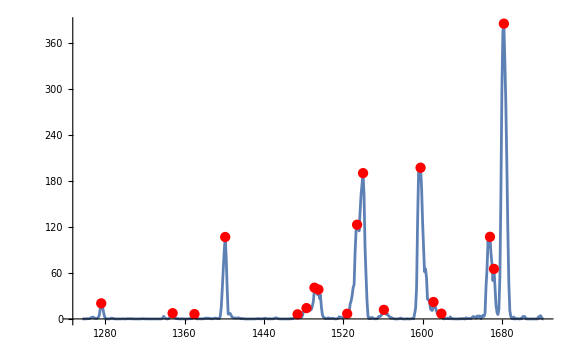

1276
1348
1370
1401
1474
1483
1491
1495
1524
1534
1540
1561
1598
1611
1619
1668
1672
1682

```mathematica
peaks=FindPeaks[data[[All,2]],0.6,2,5]
peaklist=peaks[[All,1]]
peakpos=data[[peaklist]]
Show[
ListLinePlot[data,PlotRange->Full, ImageSize->Large],
ListPlot[peakpos,PlotStyle->Red]]
peakpos[[All,1]]//TableForm
```